# Audio from noisy undersampled oscillograph

From Nov 1923 Popular Science article on telephony, The Great American Voice by R. W. King, editor Bell System Technical Journal.
The article includes a reproduction of an oscillograph trace, originally 3 feet long, rendered as two strips each as wide as a page.

The trace appeared  in the original article in two "strips".  I cut them out of the rendered page using a screenshot utility.
The result is two PNG files, which are unfortunately not the same height, even  though they represent the same range of amplitudes.

```mathematica
names = Array["/home/mg/Documents/oscillograph/america-c"<>ToString[#]<>".PNG"&,2];
stripImages=Import/@names;
stripImages
```

{-Graphics-,-Graphics-}

Our strategy will take advantage of the fact that the oscillograph trace
is truly a single-valued function, because the beam scans left to right and never
"doubles back" to the left.  That means that for each instant of time,
the trace has exactly one scalar value.

Our task then is to extract that scalar value for each time instant.
We can do that more easily if we have each vertical slice of the strip available as an array.
We turn the raw strip images into one vertical strip, as
a 2D array of scalar brightness values.  As a vertical strip, each row
represents an instant in time,  and the row happens to be the "vertical slice" values we wanted.

However, we're not working with the original oscillograph.  We have an imperfect rendering
of it that has been printed (through a halftone screen?) and then scanned (by Google).
Therefore, we may find that each row doesn't have a single peak, because the signal
from successive instants may have been smeared.

Because the scanned strips are not the same size, we operate on them in parallel here at first.
We convert them to Grayscale, so we can treat them as a single channel.
ImageData turns the single-channel image into a 2D array of scalar brightness values.

```mathematica
stripImagesGray=Map[ColorConvert[#,"Grayscale"]&,  stripImages];
d=Map[ImageData[#,Interleaving->False]&,stripImagesGray];
vertStrips =Map[Transpose[#]&,d];
```

Now we have the two strips, as a pair of 2D arrays, in the array cols.  To see this, we convert them to images.

```mathematica
Map[Image[#]&,vertStrips]
```

{-Graphics-,-Graphics-}

Now we join the two 2D arrays into one.  Because  they're different widths, we right-pad the shorter rows with zeros
so all rows are the same width as the widest one.

```mathematica
vertStrip = Join@@vertStrips;
maxwidth = Max[Length /@ vertStrip];
vertStrip = Map[PadRight[#, maxwidth]&, vertStrip];
```

```mathematica
Image[vertStrip]
```

-Graphics-

```mathematica
whereMax[x_]:=Position[x,Max[x]][[1]][[1]];
sigg[cols_]:=Array[whereMax[MovingAverage[cols[[#]],2]] &,Length[cols]];
signal=sigg[vertStrip];
```

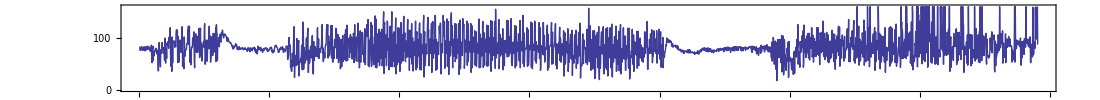

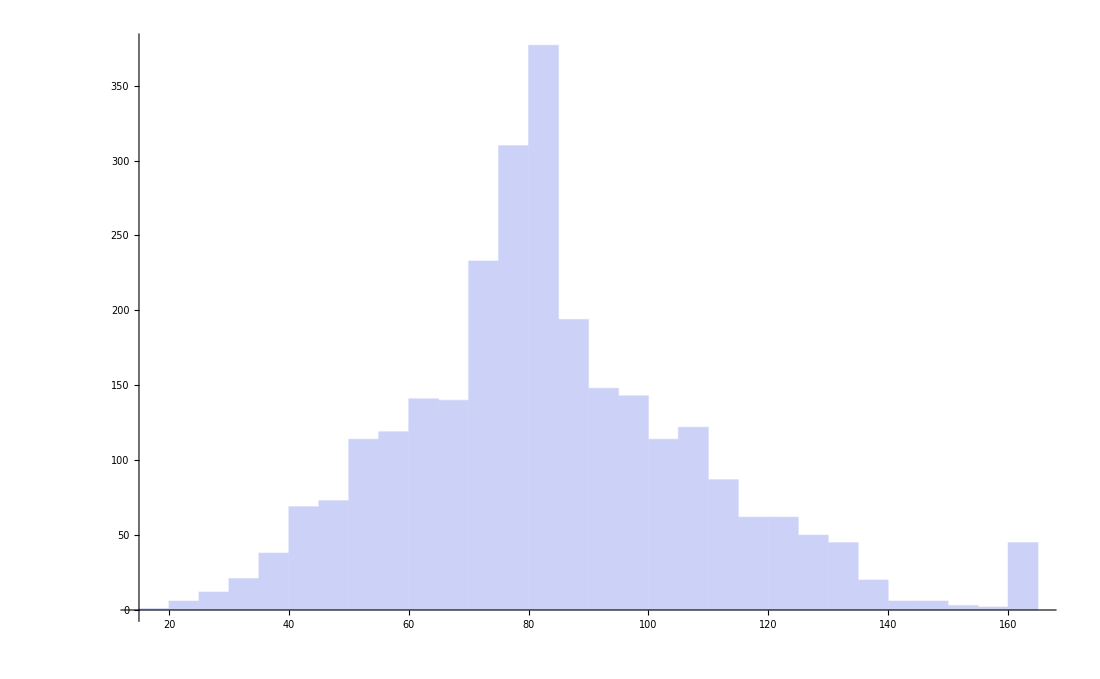

```mathematica
ListPlot[signal,ImageSize->{1100,100},Frame->True,AspectRatio->Automatic,Joined->True]
Histogram[signal]
```

```mathematica
norm[sig_]:=Map[(# - 80)/82&, sig];
snd = Sound[SampledSoundList[norm[signal], 2800]];
```

```mathematica
Export["america.wav",  snd, "WAV"]
```

america.wav

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["america.wav"]]]
```

```mathematica
ListPlay[signal,SampleRate->2800]
```

-Graphics-

Exploring the data

```mathematica
c=vertStrip[[1]]
```

{0.0941176,0.121569,0.156863,0.176471,0.176471,0.172549,0.176471,0.184314,0.196078,0.152941,0.137255,0.145098,0.152941,0.164706,0.14902,0.109804,0.101961,0.117647,0.117647,0.121569,0.129412,0.105882,0.0862745,0.0980392,0.133333,0.133333,0.137255,0.145098,0.14902,0.152941,0.156863,0.156863,0.168627,0.192157,0.207843,0.2,0.188235,0.184314,0.184314,0.184314,0.207843,0.2,0.176471,0.160784,0.172549,0.211765,0.239216,0.254902,0.168627,0.172549,0.207843,0.219608,0.2,0.192157,0.203922,0.188235,0.231373,0.231373,0.207843,0.196078,0.215686,0.219608,0.203922,0.188235,0.196078,0.2,0.219608,0.239216,0.239216,0.227451,0.235294,0.254902,0.262745,0.266667,0.423529,0.67451,0.835294,0.858824,0.807843,0.737255,0.792157,0.847059,0.890196,0.905882,0.839216,0.65098,0.443137,0.356863,0.360784,0.364706,0.388235,0.388235,0.368627,0.360784,0.345098,0.305882,0.333333,0.266667,0.239216,0.247059,0.247059,0.227451,0.196078,0.14902,0.160784,0.2,0.219608,0.180392,0.176471,0.247059,0.258824,0.180392,0.211765,0.168627,0.156863,0.180392,0.192157,0.156863,0.117647,0.105882,0.117647,0.0901961,0.0941176,0.164706,0.2,0.14902,0.12549,0.172549,0.207843,0.176471,0.145098,0.12549,0.105882,0.0980392,0.121569,0.156863,0.172549,0.172549,0.176471,0.196078,0.223529,0.223529,0.25098,0.313725,0.219608,0.156863,0.145098,0.188235,0.235294,0.25098,0.223529,0.172549,0.176471,0.176471,0.14902,0.121569,0.145098,0.211765,0.235294,0.215686,0,0,0}

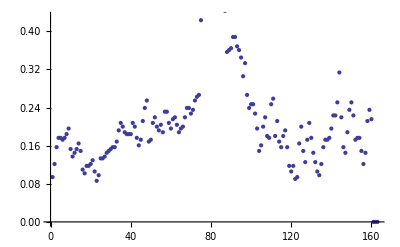

```mathematica
ListPlot[c]
```

```mathematica
Manipulate[
Show[
ListPlot[{MovingAverage[vertStrip[[in]],5]},PlotRange->1.0],
ListPlot[{Position[vertStrip[[in]],Max[vertStrip[[in]]]][[1]][[1]],1},PlotRange->{Length[vertStrip[[in]]],1.0}]
],
{in,1,Length[vertStrip],1}]
```

```mathematica
chunk =Take[vertStrip,{1,100},{15,120}];
Manipulate[
im = Image[chunk];
im =Sharpen[im,s];
ImageResize[im,1200],
{s,0,10,1}
]
```